# U-V Table

by K. ITO on 2012 - 07 - 04

目的：
StopBandDist_Sin+DC_5V0.vi用ににU-VのTableを作成する．
入力箇所は赤字で書いてある．

1V0からの変更点:
　・これまでは理論と実測のチューンのずれをroに押し付けていたが，Calibration Factorを用いるように変更した．
　・tpとCal factをヘッダに追加する．

## Initialize

```mathematica
$HistoryLength=3;
ClearAll["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

### Trap Parameters

```mathematica
ro=5.00*10^-3(*[m]:radius of Trap region*);
ff=1.00*^6;
calfct=0.967050002195;
(*calfct=0.9536(*Calibration factor estimated by Kz. ITO on 2017-02-07 for Sin wave*);*)
(*calfct=0.9560(*Calibration factor estimated by Kz. ITO on 2016-08-04 for Sin wave*);*)
(*calfct=0.9555(*Calibration factor estimated with exp. data on 2014-02-28 (Sin&FODO)*);*)
(*calfac=0.9703(*Calibration factor estimated with exp. data on 2014-09-25 (FDDF)*);*)
```

### Physical Constants

```mathematica
cc=2.99792458*10^8;(*[m/s]:Velocity of light*)
ee=1.60217733*10^-19;(*[C]:Charge*)
mu=1.6605*10^-27(*Unified atomic mass unit*);
mnar=39.948(*atomic weight of Ar*);
```

```mathematica
ClearAll[ei,mi];
ei=1*ee;
mi=mnar*mu;
tp=1/ff;
```

## Functions

### MathieuParameters

```mathematica
kkf=(calfct*ei)/(mi*ro^2*(2*Pi*ff)^2);
af[u_]:=8.0*kkf*u;
qf[v_]:=4.0*kkf*v;
```

### Tune&Phase Advance

Matheiu方程式で表される運動の Tune.

```mathematica
tune[a_,q_]:=MathieuCharacteristicExponent[a,q]/2;
```

### Sci Form

```mathematica
sciform[x_,prc_]:=ToString[
SetPrecision[
ScientificForm[x,NumberFormat->(If[Abs[ToExpression[#3]]≥1,Row[{#1,"e",#3}],Row[{#1,"e",#3}],Row[{#1,"e","0"}]]&)]
,prc]
];
```

## U-V Table ν_y=αν_x+β

### Input

```mathematica
dnx=1.0*10^-3(*nuxの変化の幅*);
nxrg={0.10,0.43}(*nuxの範囲*);
nyrg={0.0,0.5}(*nuyの範囲*);
```

```mathematica
alpha=1.0;
beta=0.;
```

### Calculation

Data Length= | 331

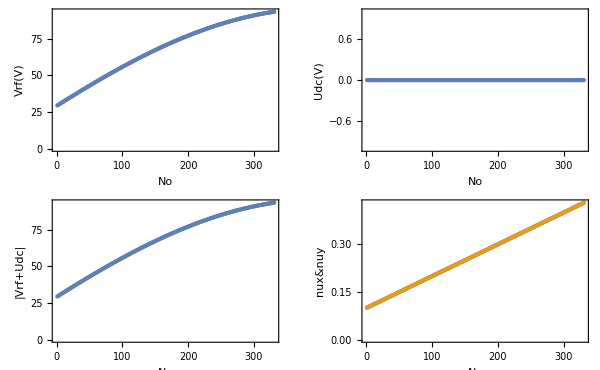

```mathematica
u0=1;
v0=50;
rt=Table[
nuy=alpha*nux+beta;
If[nyrg[[2]]≥nuy≥nyrg[[1]],
sol=FindRoot[{tune[af[uo],qf[vo]]==nux,tune[af[-uo],qf[vo]]==nuy},{{vo,v0},{uo,u0}}];
us=uo/.sol;u0=us;
vs=vo/.sol;v0=vs;,
vs="OR";us="OR";
];
{nux,nuy,vs,-us}
,{nux,nxrg[[1]],nxrg[[2]],dnx}];
rt=Chop[Delete[rt,Position[rt[[All,3]],"OR"]],1*^-8];
rt=Join[rt,Partition[rt[[All,3]]+rt[[All,4]],1],2];
rt=Sort[rt,#1[[5]]<#2[[5]]&];
TableForm[{{"Data Length=",Length[rt]}}]
g1=ListPlot[rt[[All,3]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Vrf(V)"}];
g2=ListPlot[rt[[All,4]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Udc(V)"}];
g3=ListPlot[rt[[All,5]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","|Vrf+Udc|"}];
g4=ListPlot[{rt[[All,1]],rt[[All,2]]},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","nux&nuy"}];
GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->600]
```

### Confirmation

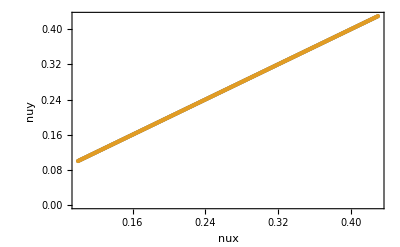

```mathematica
nut=Table[
vrf=rt[[i,3]];udc=rt[[i,4]];
nux=tune[af[udc],qf[vrf]];
nuy=tune[af[-udc],qf[vrf]];
{nux,nuy}
,{i,1,Length[rt]}];
ListPlot[{rt[[All,{1,2}]],nut},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"nux","nuy"}]
```

### Export

最後にtableを書き出す．

```mathematica
rt2=Table[
t1=NumberForm[rt[[i,1]],{6,5}];
t2=NumberForm[rt[[i,2]],{6,5}];
t3=NumberForm[rt[[i,3]],{7,4}];
t4=NumberForm[rt[[i,4]],{7,4}];
{t1,t2,t3,t4}
,{i,1,Length[rt]}];
```

```mathematica
rt2d=Prepend[rt2,{"nux","nuy","V(V)","DC(V)"}];
rt2d=Prepend[rt2d,{"Cal. Fct.=",NumberForm[N[calfct],{7,4}]}];
rt2d=Prepend[rt2d,{"Sin@tp(S/cell)=",sciform[tp,3]}];
Export["V-DC.txt",rt2d,"CSV"];
```

## U-V Table ν_y=Const

### Input

まずはnuyと計算するtuneの範囲を定義する．

```mathematica
(*nxrg={0.22,0.36,0.001}/0.955(*nuxの範囲*);
ny=0.23/0.955(*nuyの値*);*)
```

```mathematica
nxrg={0.21,0.30,0.0005}(*nuxの範囲*);
ny=0.21(*nuyの値*);
```

```mathematica
no=(nxrg[[2]]-nxrg[[1]])/nxrg[[3]];
TableForm[{{"No. =",no}}]
```

No. = | 180.

### Calculation

Data Length= | 181

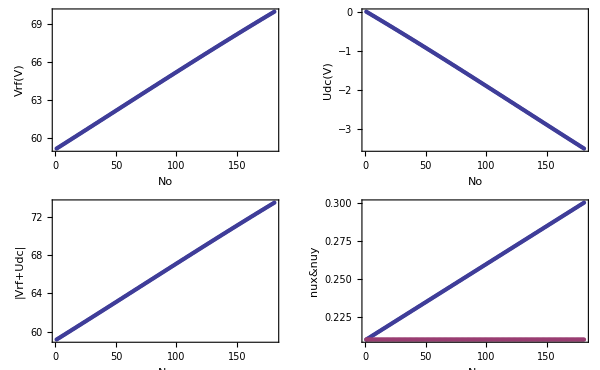

```mathematica
u0=1;
v0=50;
rt=Table[
nuy=ny;
sol=FindRoot[{tune[af[uo],qf[vo]]==nux,tune[af[-uo],qf[vo]]==nuy},{{vo,v0},{uo,u0}}];
us=uo/.sol;u0=us;
vs=vo/.sol;v0=vs;
{nux,nuy,vs,-us,vs+Abs[us]}
,{nux,nxrg[[1]],nxrg[[2]],nxrg[[3]]}];
rt=Sort[Chop[rt,1*^-8],#1[[5]]<#2[[5]]&];
TableForm[{{"Data Length=",Length[rt]}}]
g1=ListPlot[rt[[All,3]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Vrf(V)"}];
g2=ListPlot[rt[[All,4]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Udc(V)"}];
g3=ListPlot[rt[[All,5]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","|Vrf+Udc|"}];
g4=ListPlot[{rt[[All,1]],rt[[All,2]]},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","nux&nuy"}];
GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->600]
```

```mathematica
Sqrt[73.^2-2^2]
```

72.9726

### Confirmation

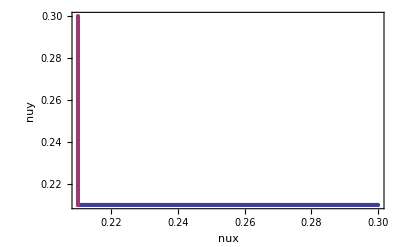

```mathematica
nut=Table[
vrf=rt[[i,3]];udc=rt[[i,4]];
nux=tune[af[udc],qf[vrf]];
nuy=tune[af[-udc],qf[vrf]];
{nux,nuy}
,{i,1,Length[rt]}];
ListPlot[{rt[[All,{1,2}]],nut},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"nux","nuy"}]
```

### Export

最後にtableを書き出す．

```mathematica
rt2=Table[
t1=NumberForm[rt[[i,1]],{6,5}];
t2=NumberForm[rt[[i,2]],{6,5}];
t3=NumberForm[rt[[i,3]],{7,4}];
t4=NumberForm[rt[[i,4]],{7,4}];
{t1,t2,t3,t4}
,{i,1,Length[rt]}];
```

```mathematica
Export["V-DC.txt",Prepend[rt2,{"nux","nuy","V(V)","DC(V)"}],"CSV"];
```

## U-V Table ν_x=Const

### Input

まずはnuyと計算するtuneの範囲を定義する．

```mathematica
nyrg={0.14,0.40,0.001}(*nuxの範囲*);
nx=0.21(*nuyの値*);
```

```mathematica
no=(nyrg[[2]]-nyrg[[1]])/nyrg[[3]];
TableForm[{{"No. =",no}}]
```

No. = | 260.

### Calculation

Data Length= | 261

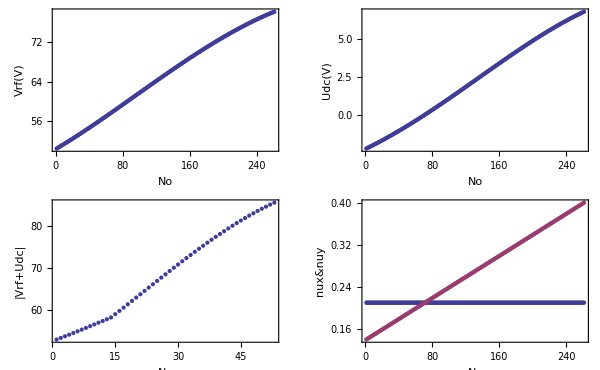

```mathematica
u0=1;
v0=50;
rt=Table[
nux=nx;
sol=FindRoot[{tune[af[uo],qf[vo]]==nux,tune[af[-uo],qf[vo]]==nuy},{{vo,v0},{uo,u0}}];
us=uo/.sol;u0=us;
vs=vo/.sol;v0=vs;
{nux,nuy,vs,-us,vs+Abs[us]}
,{nuy,nyrg[[1]],nyrg[[2]],nyrg[[3]]}];
rt=Sort[Chop[rt,1*^-8],#1[[5]]<#2[[5]]&];
TableForm[{{"Data Length=",Length[rt]}}]
g1=ListPlot[rt[[All,3]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Vrf(V)"}];
g2=ListPlot[rt[[All,4]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Udc(V)"}];
g4=ListPlot[{rt[[All,1]],rt[[All,2]]},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","nux&nuy"}];
GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->600]
```

### Confirmation

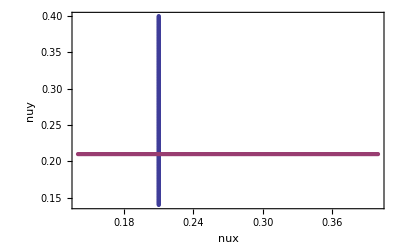

```mathematica
nut=Table[
vrf=rt[[i,3]];udc=rt[[i,4]];
nux=tune[af[udc],qf[vrf]];
nuy=tune[af[-udc],qf[vrf]];
{nux,nuy}
,{i,1,Length[rt]}];
ListPlot[{rt[[All,{1,2}]],nut},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"nux","nuy"}]
```

### Export

最後にtableを書き出す．

```mathematica
rt2=Table[
t1=NumberForm[rt[[i,1]],{6,5}];
t2=NumberForm[rt[[i,2]],{6,5}];
t3=NumberForm[rt[[i,3]],{7,4}];
t4=NumberForm[rt[[i,4]],{7,4}];
{t1,t2,t3,t4}
,{i,1,Length[rt]}];
```

## U-V Table Uniform

### Input

```mathematica
dd=0.001;
nxrg={0.234,0.289,dd}(*nuxの範囲*);
nyrg={0.234,0.289,dd}(*nuyの範囲*);
```

```mathematica
nxt=Table[i,{i,nxrg[[1]],nxrg[[2]],nxrg[[3]]}];
nyt=Table[i,{i,nyrg[[1]],nyrg[[2]],nyrg[[3]]}];
ixo=Length[nxt];
iyo=Length[nyt];
TableForm[{{"ixo=",ixo},{"iny=",iyo}}]
```

ixo= | 56
iny= | 56

### Calculation

Data Length= | 3136

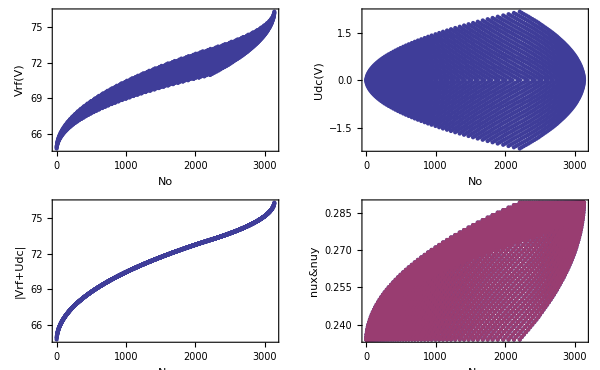

```mathematica
u0=1;
v0=50;
rt=Table[
nux=nxt[[ix]];
nuy=nyt[[iy]];
sol=FindRoot[{tune[af[uo],qf[vo]]==nux,tune[af[-uo],qf[vo]]==nuy},{{vo,v0},{uo,u0}}];
us=uo/.sol;u0=us;
vs=vo/.sol;v0=vs;
{nux,nuy,vs,-us,vs+Abs[us]}
,{ix,1,ixo},{iy,1,iyo}];
rt=Sort[Flatten[Chop[rt,1*^-8],1],#1[[5]]<#2[[5]]&];
TableForm[{{"Data Length=",Length[rt]}}]
g1=ListPlot[rt[[All,3]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Vrf(V)"}];
g2=ListPlot[rt[[All,4]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","Udc(V)"}];
g3=ListPlot[rt[[All,5]],PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","|Vrf+Udc|"}];
g4=ListPlot[{rt[[All,1]],rt[[All,2]]},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"No","nux&nuy"}];
GraphicsGrid[{{g1,g2},{g3,g4}},ImageSize->600]
```

### Confirmation

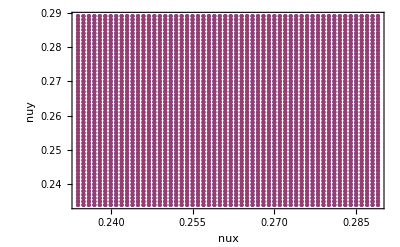

```mathematica
nut=Table[
vrf=rt[[i,3]];udc=rt[[i,4]];
nux=tune[af[udc],qf[vrf]];
nuy=tune[af[-udc],qf[vrf]];
{nux,nuy}
,{i,1,Length[rt]}];
ListPlot[{rt[[All,{1,2}]],nut},PlotRange->All,Axes-> False,Frame->True,FrameLabel->{"nux","nuy"}]
```

### Export

最後にtableを書き出す．

```mathematica
rt2=Table[
t1=NumberForm[rt[[i,1]],{6,5}];
t2=NumberForm[rt[[i,2]],{6,5}];
t3=NumberForm[rt[[i,3]],{7,4}];
t4=NumberForm[rt[[i,4]],{7,4}];
{t1,t2,t3,t4}
,{i,1,Length[rt]}];
```

```mathematica
Export["V-DC.txt",Prepend[rt2,{"nux","nuy","V(V)","DC(V)"}],"CSV"];
```

## V&DC Table etc

VrfとUdcを直接指定する．

### Input

```mathematica
rt=Table[{0,0,vv,0},{vv,10,92,0.2}];
```

```mathematica
Length[rt]
```

411

### Confirmation

### Export

最後にtableを書き出す．

```mathematica
rt2=Table[
t1=NumberForm[rt[[i,1]],{6,5}];
t2=NumberForm[rt[[i,2]],{6,5}];
t3=NumberForm[rt[[i,3]],{7,4}];
t4=NumberForm[rt[[i,4]],{7,4}];
{t1,t2,t3,t4}
,{i,1,Length[rt]}];
```

```mathematica
rt2d=Prepend[rt2,{"nux","nuy","V(V)","DC(V)"}];
Export["V-DC.txt",rt2d,"CSV"];
```

```mathematica
1/0.12
```

8.33333

```mathematica
1/12.
```

0.0833333

```mathematica
0.15*360
```

54.

```mathematica
0.3*360
```

108.

```mathematica
50/360.
```

0.138889

```mathematica
110/360.
```

0.305556

```mathematica
420*10/3600.
```

1.16667

```mathematica
22*22*4
```

1936

```mathematica
0.25/0.265
```

0.943396

```mathematica
0.02/0.25*100
```

8.